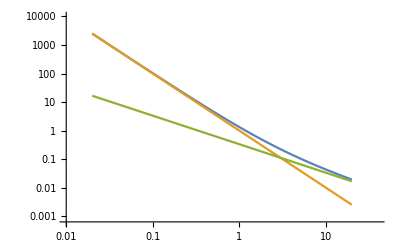

```mathematica
LogLogPlot[{1/r^2*(1+r/3),1/r^2,1/(3r)},{r,0.1/5,100.0/5}]
```

```mathematica
D[-Expand[1/r^2*(1+r/3)],r]
```

2/r^3+1/(3 r^2)

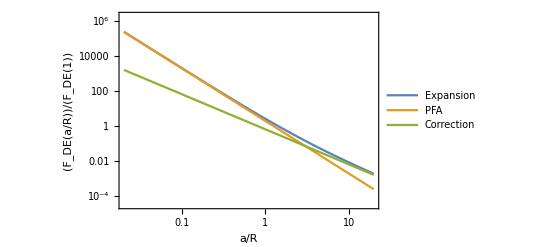

```mathematica
LogLogPlot[{2/r^3*(1+r/3),2/r^3,2/(3r^2)},{r,0.1/5,100.0/5},FrameLabel->{a/R//InputForm,Subscript[F, DE][a/R]/Subscript[F, DE][1]},Frame->True,PlotRange->{{0.1/5,100.0/5},Full},PlotLegends->{"Expansion","PFA","Correction"}]
```